```mathematica
x0=0.;
y0=0.;
vx0 =V Cos[th];
vy0=V Sin[th];
vter=Sqrt[m g/ c];

ode1={x''[t] ==  -g (x'[t] / (vter^2)) Sqrt[(x'[t])^2 + (y'[t])^2],y''[t]==  -g (1+  (y'[t] / (vter^2)) Sqrt[(x'[t])^2 + (y'[t])^2] ),x[0]== x0,x'[0]==  vx0, y[0]== y0, y'[0] ==  vy0}/.{V->100,th->50*(Pi/180),m->1,g->9.8,c->0.002};

sol=NDSolve[ode1,{x,y},{t,0,200}];
sol
```

{{x→InterpolatingFunction[{{0.,200.}},<>],y→InterpolatingFunction[{{0.,200.}},<>]}}

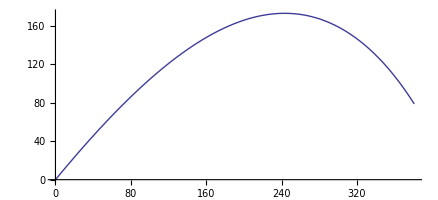

```mathematica
projplot1 = ParametricPlot[Evaluate[{x[t],y[t]}/.sol],{t,0,10}];
Show[projplot1]
```

```mathematica
Manipulate[
vx0 =V Cos[th*Pi/180];vy0=V* Sin[th*Pi/180];vter=Sqrt[2 m gg/ (c ρairVar A)];ρair = 1.29 (*kg /(meters^3)*);x0=0.;g = 9.8 ;(*gravitational constant m/(seconds)^2*);
ode1={x''[t] ==  -gg (x'[t] / (vter^2)) Sqrt[(x'[t])^2 + (y'[t])^2],y''[t]==  -gg(1+  (y'[t] / (vter^2)) Sqrt[(x'[t])^2 + (y'[t])^2] ),x[0]== x0,x'[0]==  vx0, y[0]== y0, y'[0] ==  vy0};

sol=NDSolve[ode1,{x,y},{t,0,200}]; ParametricPlot[Evaluate[{x[t],y[t]}/.sol],{t,0,tmax},PlotRange->{{0,maxrange[[1]]},{0,maxrange[[2]]}},AxesLabel->{"t (s)","θ (rad)"},ImageSize->{700,500}],Style["Launch parameters",12,Bold],
{{V,100.,"Initial speed(m/s)"},0.,600.,Appearance->"Labeled"},{{th,50.,"initial angle (degrees)"},0.,90.,Appearance->"Labeled"},
{{y0,0.,"initial launch height"},0.,10.,Appearance->"Labeled"},
Delimiter,
Style["Projectile properties",12,Bold],
{{m,1.,"Projectile mass {kg)"},0.000000001,100.,Appearance->"Labeled"},{{A,0.001,"Projectile cross-section area (m^2)"},0.0000001,50.,Appearance->"Labeled"},
{{c,0.5,"Coefficient of quadratic drag"},0.001,10.0,Appearance->"Labeled"},
Delimiter,
Style["Physical Environment",12,Bold],{{gg,g,"gravitational acceleration"},0.1 g,10 g,Appearance->"Labeled"},
{{ρairVar,ρair,"Density of air (kg /meters^3)"},0.1 ρair,10 ρair,Appearance->"Labeled"},{{tmax,200,"Duration of object existance (aka flight duration pictured, s)"},10,400,Appearance->"Labeled"},
{{maxrange,{100,100},"plot window scale/ axes range"},{1.,1.},{1000.,1000.},Appearance->"Labeled"},
ControlPlacement->Top]
```